```mathematica
Parametrization of GPDs used in GK model for pi0 production
```

for GK GPDs in model of Parametrization pi0 production used

```mathematica
\tilde{H}
```

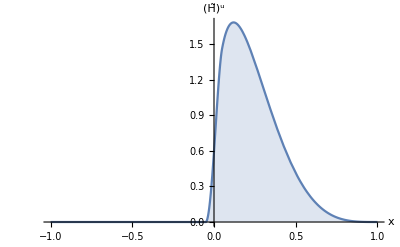

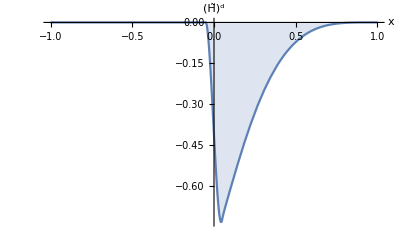

```mathematica
cu=List[cu=0.213,0.929,12.59,-12.57,0.0];
cd=List[cd=-0.204,-0.940,-0.314,1.524,0.0];
pu[y_]:=y^(-0.32)*(1-y)^0*(0.213+0.929*Sqrt[y]+12.59*y-12.57*y^(3/2)+0.0*y^2);
pd[y_]:=y^(-0.32)*(1-y)^0*(-0.204-0.940*Sqrt[y]-0.314*y+1.524*y^(3/2)+0.0*y^2);
fu[y_]:=(-0.961*Log[y]+0.545)*(1-y)^3+(1.264)*y*(1-y)^2;
fd[y_]:=(-0.861*Log[y]+0.206)*(1-y)^3+(4.198)*y*(1-y)^2;

lowery[x_,xi_]:=HeavisideTheta[x-xi]*(x-xi)/(1-xi);
uppery[x_,xi_]:=HeavisideTheta[x+xi]*(x+xi)/(1+xi);

Htildeu[x_,xi_,t_]:=3/(4*xi^3)*NIntegrate[pu[y]*Exp[t*fu[y]]*(xi^2*(1-y)^2-(x-y)^2),{y,lowery[x,xi],uppery[x,xi]}];
Htilded[x_,xi_,t_]:=3/(4*xi^3)*NIntegrate[pd[y]*Exp[t*fd[y]]*(xi^2*(1-y)^2-(x-y)^2),{y,lowery[x,xi],uppery[x,xi]}];

Plot[Htildeu[x,0.05,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(H̃)^u"},Filling->Axis]

Plot[Htilded[x,0.05,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(H̃)^d"},Filling->Axis]
```

## \tilde{E}

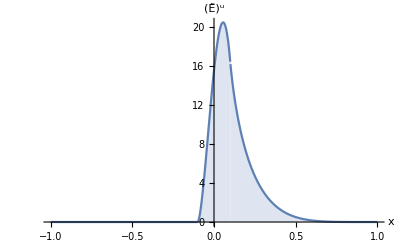

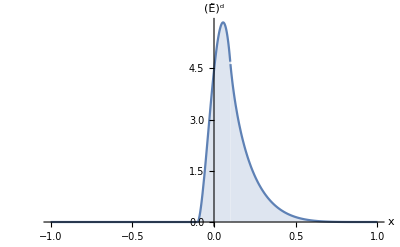

```mathematica
EtildeAlpha0=0.32;
EtildeAlphaprime=0.45;
Etildeb=0.9;
EtildeNu=14;
EtildeNd=4;

k[t_]=EtildeAlpha0+EtildeAlphaprime*t;

(*When x+xi < 0.0*)
D1=0.0;
(*When x-xi < 0.0*)
D2[i_,x_,xi_,t_]:=3/(2*xi^3)*((x+xi)/(1+xi))^(2+i-k[t])*(xi^2-x+(2+i-k[t])*xi*(1-x))/((1+i-k[t])*(2+i-k[t])*(3+i-k[t]));
(*Else*)
D3[i_,x_,xi_,t_]:=3/(2*xi^3)/((1+i-k[t])*(2+i-k[t])*(3+i-k[t]))*((xi^2-x)*(((x+xi)/(1+xi))^(2+i-k[t])-((x-xi)/(1-xi))^(2+i-k[t]))+xi*(1-x)*(2+i-k[t])*(((x+xi)/(1+xi))^(2+i-k[t])+((x-xi)/(1-xi))^(2+i-k[t])));

DD[i_,x_,xi_,t_]= If[x<-xi,D1,If[-xi≤x≤xi,D2[i,x,xi,t],D3[i,x,xi,t]]];

Etildeu[x_,xi_,t_]:=Exp[Etildeb*t]*(EtildeNu*DD[0,x,xi,t]-2*EtildeNu*DD[1,x,xi,t]+EtildeNu*DD[2,x,xi,t]);
Etilded[x_,xi_,t_]:=Exp[Etildeb*t]*(EtildeNd*DD[0,x,xi,t]-2*EtildeNd*DD[1,x,xi,t]+EtildeNd*DD[2,x,xi,t]);


Plot[Etildeu[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ẽ)^u"},Filling->Axis]

Plot[Etilded[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ẽ)^d"},Filling->Axis]
```

## H_T and \bar{E}_T

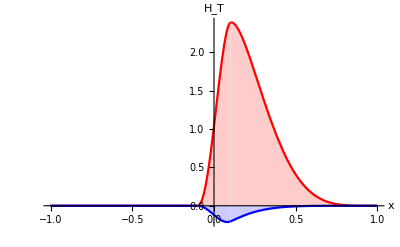

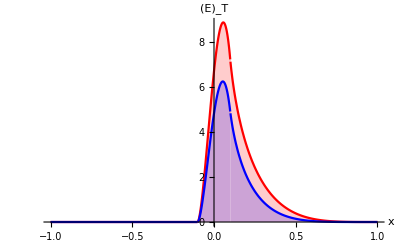

```mathematica
HTAlpha0u=-0.17;
HTAlphaprimeu=0.45;
HTbu=0.0;

HTAlpha0d=-0.17;
HTAlphaprimed=0.45;
HTbd=0.0;

HTNu=1.1;
HTNd=-0.3;

EbarTAlpha0u=0.3;
EbarTAlpha0d=0.3;
EbarTAlphaprimeu=0.45;
EbarTAlphaprimed=0.45;
EbarTbu=0.5;
EbarTbd=0.5;
EbarTNu=4.83;
EbarTNd=3.57;

HTku[t_]=HTAlpha0u+HTAlphaprimeu*t;
HTkd[t_]=HTAlpha0d+HTAlphaprimed*t;
ku[t_,i_]:=2+i-HTku[t];
kd[t_,i_]:=2+i-HTkd[t];

EbarTku[t_]=EbarTAlpha0u+EbarTAlphaprimeu*t;
EbarTkd[t_]=EbarTAlpha0d+EbarTAlphaprimed*t;
mu[t_,i_]:=2+i-EbarTku[t];
md[t_,i_]:=2+i-EbarTkd[t];

(*When x+ξ < 0.0*)
HTD1u=0.0;
(*When x-ξ < 0.0
HTD2uold[i_,x_,ξ_,t_]:=3/(2*ξ^3)*((x+ξ)/(1+ξ))^ku[t,i]*(ξ^2-x+ku[t,i]*ξ*(1-x))/((-1+ku[t,i])*ku[t,i]*(1+ku[t,i]));*)

HTD2u[i_,x_,ξ_,t_]:=(3 ((x+ξ)/(1+ξ))^ku[t,i] (ξ^2-x+(ξ-x ξ) ku[t,i]))/(2 ξ^3 ku[t,i] (ku[t,i]^2-1));
(*Else
HTD3uold[i_,x_,ξ_,t_]:=3/(2*ξ^3)/((ku[t,i]-1)*(ku[t,i])*(ku[t,i]+1))*((ξ^2-x)*(((x+ξ)/(1+ξ))^(ku[t,i])-((x-ξ)/(1-ξ))^(ku[t,i]))+ξ*(1-x)*(ku[t,i])*(((x+ξ)/(1+ξ))^(ku[t,i])+((x-ξ)/(1-ξ))^(ku[t,i])));*)

HTD3u[i_,x_,ξ_,t_]:=(3 (x-ξ^2) (((ξ-x)/(ξ-1))^ku[t,i]-((x+ξ)/(1+ξ))^ku[t,i])-3 (x-1) ξ (((ξ-x)/(ξ-1))^ku[t,i]+((x+ξ)/(1+ξ))^ku[t,i]) ku[t,i])/(2 ξ^3 ku[t,i] (ku[t,i]^2-1));
(*
HTDDu1[i_,x_,ξ_,t_]= If[x<-ξ,HTD1u,If[-ξ≤x≤ξ,HTD2u[i,x,ξ,t],HTD3u[i,x,ξ,t]]];
HTDDu[i_,x_,ξ_,t_]=If[ξ<0.01,HTDDuser[i,x,ξ,t],HTDDu1[i,x,ξ,t]];
*)
HTD1d=0.0;
(*When x-ξ < 0.0
HTD2dold[i_,x_,ξ_,t_]:=3/(2*ξ^3)*((x+ξ)/(1+ξ))^kd[t,i]*(ξ^2-x+ku[t,i]*ξ*(1-x))/((-1+kd[t,i])*kd[t,i]*(1+kd[t,i]));*)
HTD2d[i_,x_,ξ_,t_]:=(3 ((x+ξ)/(1+ξ))^kd[t,i] (-x+ξ^2+(ξ-x ξ) ku[t,i]))/(2 ξ^3 kd[t,i] (-1+kd[t,i]^2));
(*Else
HTD3dold[i_,x_,ξ_,t_]:=3/(2*ξ^3)/((kd[t,i]-1)*(kd[t,i])*(kd[t,i]+1))*((ξ^2-x)*(((x+ξ)/(1+ξ))^(kd[t,i])-((x-ξ)/(1-ξ))^(kd[t,i]))+ξ*(1-x)*(kd[t,i])*(((x+ξ)/(1+ξ))^(kd[t,i])+((x-ξ)/(1-ξ))^(kd[t,i])));*)
HTD3d[i_,x_,ξ_,t_]:=(3 (x-ξ^2) (((-x+ξ)/(-1+ξ))^kd[t,i]-((x+ξ)/(1+ξ))^kd[t,i])-3 (-1+x) ξ (((-x+ξ)/(-1+ξ))^kd[t,i]+((x+ξ)/(1+ξ))^kd[t,i]) kd[t,i])/(2 ξ^3 kd[t,i] (-1+kd[t,i]^2));
(*
HTDDd1[i_,x_,ξ_,t_]= If[x<-ξ,HTD1d,If[-ξ≤x≤ξ,HTD2d[i,x,ξ,t],HTD3d[i,x,ξ,t]]];
HTDDd[i_,x_,ξ_,t_]=If[ξ<0.01,HTDDdser[i,x,ξ,t],HTDDd1[i,x,ξ,t]];
*)
(*===============================   E  b a r  T  =============================*)
(*When x+ξ < 0.0*)
EbarTD1u=0.0;
(*When x-ξ < 0.0
EbarTD2uold[i_,x_,ξ_,t_]:=3/(2*ξ^3)*((x+ξ)/(1+ξ))^(mu[t,i])*(ξ^2-x+(mu[t,i])*ξ*(1-x))/((mu[t,i]-1)*(mu[t,i])*(mu[t,i]+1));*)
EbarTD2u[i_,x_,ξ_,t_]:=(3 ((x+ξ)/(1+ξ))^mu[t,i] (-x+ξ^2+(ξ-x ξ) mu[t,i]))/(2 ξ^3 mu[t,i] (-1+mu[t,i]^2));
(*Else
EbarTD3uold[i_,x_,ξ_,t_]:=3/(2*ξ^3)/((mu[t,i]-1)*(mu[t,i])*(mu[t,i]+1))*((ξ^2-x)*(((x+ξ)/(1+ξ))^(mu[t,i])-((x-ξ)/(1-ξ))^(mu[t,i]))+ξ*(1-x)*(mu[t,i])*(((x+ξ)/(1+ξ))^(mu[t,i])+((x-ξ)/(1-ξ))^(mu[t,i])));*)
EbarTD3u[i_,x_,ξ_,t_]:=(3 (x-ξ^2) (((-x+ξ)/(-1+ξ))^mu[t,i]-((x+ξ)/(1+ξ))^mu[t,i])-3 (-1+x) ξ (((-x+ξ)/(-1+ξ))^mu[t,i]+((x+ξ)/(1+ξ))^mu[t,i]) mu[t,i])/(2 ξ^3 mu[t,i] (-1+mu[t,i]^2));
(*
EbarTDDu1[i_,x_,ξ_,t_]= If[x<-ξ,EbarTD1u,If[-ξ≤x≤ξ,EbarTD2u[i,x,ξ,t],EbarTD3u[i,x,ξ,t]]];
EbarTDDu[i_,x_,ξ_,t_]=If[ξ<0.01,EbarTDDuser[i,x,ξ,t],EbarTDDu1[i,x,ξ,t]];
*)

(*When x+ξ < 0.0*)
EbarTD1d=0.0;
(*When x-ξ < 0.0
EbarTD2dold[i_,x_,ξ_,t_]:=3/(2*ξ^3)*((x+ξ)/(1+ξ))^(md[t,i])*(ξ^2-x+(md[t,i])*ξ*(1-x))/((md[t,i]-1)*(md[t,i])*(md[t,i]+1));*)
EbarTD2d[i_,x_,ξ_,t_]:=(3 ((x+ξ)/(1+ξ))^md[t,i] (-x+ξ^2+(ξ-x ξ) md[t,i]))/(2 ξ^3 md[t,i] (-1+md[t,i]^2));
(*Else
EbarTD3dold[i_,x_,ξ_,t_]:=3/(2*ξ^3)/((md[t,i]-1)*(md[t,i])*(md[t,i]+1))*((ξ^2-x)*(((x+ξ)/(1+ξ))^(md[t,i])-((x-ξ)/(1-ξ))^(md[t,i]))+ξ*(1-x)*(md[t,i])*(((x+ξ)/(1+ξ))^(md[t,i])+((x-ξ)/(1-ξ))^(md[t,i])));*)
EbarTD3d[i_,x_,ξ_,t_]:=(3 (x-ξ^2) (((-x+ξ)/(-1+ξ))^md[t,i]-((x+ξ)/(1+ξ))^md[t,i])-3 (-1+x) ξ (((-x+ξ)/(-1+ξ))^md[t,i]+((x+ξ)/(1+ξ))^md[t,i]) md[t,i])/(2 ξ^3 md[t,i] (-1+md[t,i]^2));
(*
EbarTDDd1[i_,x_,ξ_,t_]= If[x<-ξ,EbarTD1d,If[-ξ≤x≤ξ,EbarTD2d[i,x,ξ,t],EbarTD3d[i,x,ξ,t]]];
EbarTDDd[i_,x_,ξ_,t_]=If[ξ<0.01,EbarTDDdser[i,x,ξ,t],EbarTDDd1[i,x,ξ,t]];
*)
(*                          S E R I E S:  run HT_ETbar_series.nb            *)
EbarTDDuser[i_,x_,ξ_,t_]:=-1. (x^(-2+mu[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+mu[t,i]) mu[t,i] (-5.551115123125783*^-17+1.6653345369377348*^-16 x^2-2.7755575615628914*^-17 mu[t,i]^2)) ξ)/(-1.+mu[t,i]^2)+1/(-1.+mu[t,i]^2)x^(-4+mu[t,i]) (-0.6000000000000001+1. x-0.9999999999999999 x^4+0.6000000000000001 x^5+(0.5000000000000001-1.5000000000000009 x+1.0000000000000018 x^2+0.9999999999999979 x^3-1.4999999999999993 x^4+0.49999999999999967 x^5) mu[t,i]+(0.5-0.49999999999999994 x-0.9999999999999997 x^2+1. x^3+0.5000000000000001 x^4-0.4999999999999998 x^5) mu[t,i]^2+(-0.5000000000000001+1.5 x-0.9999999999999999 x^2-1.0000000000000002 x^3+1.5 x^4-0.5000000000000001 x^5) mu[t,i]^3+(0.1-0.5 x+0.9999999999999999 x^2-1. x^3+0.49999999999999994 x^4-0.1 x^5) mu[t,i]^4) ξ^2;

EbarTDDdser[i_,x_,ξ_,t_]:=-1. (x^(-2+md[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+md[t,i]) md[t,i] (-5.551115123125783*^-17+1.6653345369377348*^-16 x^2-2.7755575615628914*^-17 md[t,i]^2)) ξ)/(-1.+md[t,i]^2)+1/(-1.+md[t,i]^2)x^(-4+md[t,i]) (-0.6000000000000001+1. x-0.9999999999999999 x^4+0.6000000000000001 x^5+(0.5000000000000001-1.5000000000000009 x+1.0000000000000018 x^2+0.9999999999999979 x^3-1.4999999999999993 x^4+0.49999999999999967 x^5) md[t,i]+(0.5-0.49999999999999994 x-0.9999999999999997 x^2+1. x^3+0.5000000000000001 x^4-0.4999999999999998 x^5) md[t,i]^2+(-0.5000000000000001+1.5 x-0.9999999999999999 x^2-1.0000000000000002 x^3+1.5 x^4-0.5000000000000001 x^5) md[t,i]^3+(0.1-0.5 x+0.9999999999999999 x^2-1. x^3+0.49999999999999994 x^4-0.1 x^5) md[t,i]^4) ξ^2;

HTDDuser[i_,x_,ξ_,t_]:=-1. (x^(-2+ku[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+ku[t,i]) ku[t,i] (-5.551115123125783*^-17+1.6653345369377348*^-16 x^2-2.7755575615628914*^-17 ku[t,i]^2)) ξ)/(-1.+ku[t,i]^2)+1/(-1.+ku[t,i]^2)x^(-4+ku[t,i]) (-0.6000000000000001+1. x-0.9999999999999999 x^4+0.6000000000000001 x^5+(0.5000000000000001-1.5000000000000009 x+1.0000000000000018 x^2+0.9999999999999979 x^3-1.4999999999999993 x^4+0.49999999999999967 x^5) ku[t,i]+(0.5-0.49999999999999994 x-0.9999999999999997 x^2+1. x^3+0.5000000000000001 x^4-0.4999999999999998 x^5) ku[t,i]^2+(-0.5000000000000001+1.5 x-0.9999999999999999 x^2-1.0000000000000002 x^3+1.5 x^4-0.5000000000000001 x^5) ku[t,i]^3+(0.1-0.5 x+0.9999999999999999 x^2-1. x^3+0.49999999999999994 x^4-0.1 x^5) ku[t,i]^4) ξ^2;
HTDDdser[i_,x_,ξ_,t_]:=-1. (x^(-2+kd[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+kd[t,i]) kd[t,i] (-5.551115123125783*^-17+1.6653345369377348*^-16 x^2-2.7755575615628914*^-17 kd[t,i]^2)) ξ)/(-1.+kd[t,i]^2)+1/(-1.+kd[t,i]^2)x^(-4+kd[t,i]) (-0.6000000000000001+1. x-0.9999999999999999 x^4+0.6000000000000001 x^5+(0.5000000000000001-1.5000000000000009 x+1.0000000000000018 x^2+0.9999999999999979 x^3-1.4999999999999993 x^4+0.49999999999999967 x^5) kd[t,i]+(0.5-0.49999999999999994 x-0.9999999999999997 x^2+1. x^3+0.5000000000000001 x^4-0.4999999999999998 x^5) kd[t,i]^2+(-0.5000000000000001+1.5 x-0.9999999999999999 x^2-1.0000000000000002 x^3+1.5 x^4-0.5000000000000001 x^5) kd[t,i]^3+(0.1-0.5 x+0.9999999999999999 x^2-1. x^3+0.49999999999999994 x^4-0.1 x^5) kd[t,i]^4) ξ^2;

(*          E N D                 S E R I E S:  run HT_ETbar_series.nb            *)

HTDDu1[i_,x_,ξ_,t_]= If[x<-ξ,HTD1u,If[-ξ≤x≤ξ,HTD2u[i,x,ξ,t],HTD3u[i,x,ξ,t]]];
HTDDu[i_,x_,ξ_,t_]=If[ξ<0.01,HTDDuser[i,x,ξ,t],HTDDu1[i,x,ξ,t]];

HTDDd1[i_,x_,ξ_,t_]= If[x<-ξ,HTD1d,If[-ξ≤x≤ξ,HTD2d[i,x,ξ,t],HTD3d[i,x,ξ,t]]];
HTDDd[i_,x_,ξ_,t_]=If[ξ<0.01,HTDDdser[i,x,ξ,t],HTDDd1[i,x,ξ,t]];


EbarTDDu1[i_,x_,ξ_,t_]= If[x<-ξ,EbarTD1u,If[-ξ≤x≤ξ,EbarTD2u[i,x,ξ,t],EbarTD3u[i,x,ξ,t]]];
EbarTDDu[i_,x_,ξ_,t_]=If[ξ<0.01,EbarTDDuser[i,x,ξ,t],EbarTDDu1[i,x,ξ,t]];

EbarTDDd1[i_,x_,ξ_,t_]= If[x<-ξ,EbarTD1d,If[-ξ≤x≤ξ,EbarTD2d[i,x,ξ,t],EbarTD3d[i,x,ξ,t]]];
EbarTDDd[i_,x_,ξ_,t_]=If[ξ<0.01,EbarTDDdser[i,x,ξ,t],EbarTDDd1[i,x,ξ,t]];




HTu[x_,ξ_,t_]:=HTNu*Exp[HTbu*t]*(3.653*HTDDu[0,x,ξ,t]-0.583*HTDDu[0.5,x,ξ,t]+19.807*HTDDu[1,x,ξ,t]-23.487*HTDDu[1.5,x,ξ,t]-23.46*HTDDu[2,x,ξ,t]+24.07*HTDDu[2.5,x,ξ,t]);
HTd[x_,ξ_,t_]:=HTNd*Exp[HTbd*t]*(1.924*HTDDd[0,x,ξ,t]+0.179*HTDDd[0.5,x,ξ,t]-7.775*HTDDd[1,x,ξ,t]+3.504*HTDDd[1.5,x,ξ,t]+5.851*HTDDd[2,x,ξ,t]-3.683*HTDDd[2.5,x,ξ,t]);

EbarTu[x_,ξ_,t_]:=EbarTNu*Exp[EbarTbu*t]*(EbarTDDu[0,x,ξ,t]-EbarTDDu[1,x,ξ,t]);
EbarTd[x_,ξ_,t_]:=EbarTNd*Exp[EbarTbd*t]*(EbarTDDd[0,x,ξ,t]-2*EbarTDDd[1,x,ξ,t]+EbarTDDd[2,x,ξ,t]);

Plot[{HTu[x,0.1,-0.0],HTd[x,0.1,-0.0]},{x,-1.0,1.0},PlotRange->All,PlotStyle->{Red,Blue},AxesLabel->{"x","H_T"},Filling->Axis]

Plot[{EbarTu[x,0.1,-0.0],EbarTd[x,0.1,-0.0]},{x,-1.0,1.0},PlotRange->All,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"},Filling->Axis]

(*
Print["(H̃)^u t=-0.0"]
Plot3D[Htildeu[x,ξ,-0.00],{x,-1.0,1.0},{ξ,.01,1.0},AxesLabel->{"x","ξ","(H̃)^u"},PlotRange->All,ColorFunction->"DarkRainbow"]
Print["(H̃)^d t=-0.0"]
Plot3D[Htilded[x,ξ,-0.00],{x,-1.0,1.0},{ξ,.01,1.0},AxesLabel->{"x","ξ","(H̃)^u"},PlotRange->All,ColorFunction->"DarkRainbow"]

Print["((Ẽ)^u)^u t=-0.0"]
Plot3D[Etildeu[x,ξ,-0.00],{x,-1.0,1.0},{ξ,.01,1.0},AxesLabel->{"x","ξ","(Ẽ)^u"},PlotRange->All,ColorFunction->"DarkRainbow"]

Print["((Ẽ)^d)^u t=-0.0"]
Plot3D[Etilded[x,ξ,-0.00],{x,-1.0,1.0},{ξ,.01,1.0},AxesLabel->{"x","ξ","(Ẽ)^d"},PlotRange->All,ColorFunction->"DarkRainbow"]

Print["H_T^u t=-0.0"]

Plot3D[HTu[x,ξ,-0.00],{x,-1.0,1.0},{ξ,.01,1.0},AxesLabel->{"x","ξ","H_T^u"},PlotRange->All,ColorFunction->"DarkRainbow"]
Print["H_T^d t=-0.0"]
Plot3D[HTd[x,ξ,-0.0],{x,-1.0,1.0},{ξ,.01,1.0},AxesLabel->{"x","ξ","H_T^d"},PlotRange->All,ColorFunction->"DarkRainbow"]
Print["(Ē)_T^u t=-0.0"]

Plot3D[{EbarTu[x,ξ,-0.00],EbarTd[x,ξ,-0.0]},{x,-1.0,1.0},{ξ,.01,1.0},AxesLabel->{"x","ξ","(Ē)_T^u"},PlotRange->All,ColorFunction->"DarkRainbow",Filling->Axis]
Print["(Ē)_T^d t=-0.0"]
Plot3D[EbarTd[x,ξ,-0.0],{x,-1.0,1.0},{ξ,.01,1.0},AxesLabel->{"x","ξ","(Ē)_T^d"},PlotRange->All,ColorFunction->"DarkRainbow"]
*)
```

```mathematica
-1. (x^(-2+mu[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+mu[t,i]) mu[t,i] (-5.551115123125783*^-17+1.6653345369377348*^-16 x^2-2.7755575615628914*^-17 mu[t,i]^2)) ξ)/(-1.+mu[t,i]^2)+1/(-1.+mu[t,i]^2)x^(-4+mu[t,i]) (-0.6000000000000001+1. x-0.9999999999999999 x^4+0.6000000000000001 x^5+(0.5000000000000001-1.5000000000000009 x+1.0000000000000018 x^2+0.9999999999999979 x^3-1.4999999999999993 x^4+0.49999999999999967 x^5) mu[t,i]+(0.5-0.49999999999999994 x-0.9999999999999997 x^2+1. x^3+0.5000000000000001 x^4-0.4999999999999998 x^5) mu[t,i]^2+(-0.5000000000000001+1.5 x-0.9999999999999999 x^2-1.0000000000000002 x^3+1.5 x^4-0.5000000000000001 x^5) mu[t,i]^3+(0.1-0.5 x+0.9999999999999999 x^2-1. x^3+0.49999999999999994 x^4-0.1 x^5) mu[t,i]^4) ξ^2
```

-1. x^(-2+mu[t,i]) (-1.+1. x)^3-(1.5 x^(-2+mu[t,i]) ξ mu[t,i] (-5.55112×10^-17+1.66533×10^-16 x^2-2.77556×10^-17 mu[t,i]^2))/(-1.+mu[t,i]^2)+1/(-1.+mu[t,i]^2)x^(-4+mu[t,i]) ξ^2 (-0.6+1. x-1. x^4+0.6 x^5+(0.5-1.5 x+1. x^2+1. x^3-1.5 x^4+0.5 x^5) mu[t,i]+(0.5-0.5 x-1. x^2+1. x^3+0.5 x^4-0.5 x^5) mu[t,i]^2+(-0.5+1.5 x-1. x^2-1. x^3+1.5 x^4-0.5 x^5) mu[t,i]^3+(0.1-0.5 x+1. x^2-1. x^3+0.5 x^4-0.1 x^5) mu[t,i]^4)

```mathematica
ksi=0.01;
Integrate[HTu[x,ksi,0.],{x,-0.2,1}]
Integrate[HTd[x,ksi,0.],{x,-0.2,1}]
Integrate[EbarTu[x,ksi,0.],{x,-0.2,1}]
Integrate[EbarTd[x,ksi,0.],{x,-0.2,1}]
```

0.82997

-0.0520946

2.07467

1.34513

```mathematica
ksi=0.1;
Integrate[HTu[x,ksi,0.],{x,-0.2,1}]
Integrate[HTd[x,ksi,0.],{x,-0.2,1}]
Integrate[EbarTu[x,ksi,0.],{x,-0.2,1}]
Integrate[EbarTd[x,ksi,0.],{x,-0.2,1}]
```

0.82997

-0.0520946

2.07467

1.34513